```mathematica
Quit[]
```

```mathematica
$Assumptions=α∈Reals&&α>0&&m∈Reals&&m>0&&λ∈Reals;
```

```mathematica
ω[p_]:=√(m^2+p^2)-m(*p^2/(2m)*);Nx=15;max=100;
```

```mathematica
m =50/2;λ=π/2;
```

```mathematica
Clear@α
```

```mathematica
α=(*0.33375*)0.23206285465963236;
```

```mathematica
ϕ[n_][p_]:=√(α/(√π 2^n n!)) HermiteH[n,α p] E^(1/2 (-α^2) p^2)
```

```mathematica
H[n_][p_?NumberQ]:=ω[p]ϕ[n][p]-λ/π NIntegrate[(ϕ[n][k]-ϕ[n][p]-(k-p)ϕ[n]'[p])/(p-k)^2,{k,-max,0,max}]
```

```mathematica
Table[2NIntegrate[ϕ[2i][p]H[2n][p],{p,0,max},MaxRecursion->10],{i,0,Nx},{n,0,Nx}]//AbsoluteTiming
Sort@Eigenvalues[Last[%]]
```

{5271.02,{{0.384273,0.104232,-0.0450471,-0.0228966,-0.0153769,-0.011341,-0.00888438,-0.00724405,-0.00607882,-0.00521255,-0.00454577,-0.00401827,-0.00359161,-0.00324012,-0.00294605,-0.00269677},{0.118387,1.41182,0.387016,-0.0597149,-0.0234066,-0.0149291,-0.010467,-0.00791667,-0.00628219,-0.00516016,-0.00434881,-0.00373862,-0.00326527,-0.00288879,-0.00258313,-0.00233066},{-0.0450319,0.421732,2.28287,0.658237,-0.0790279,-0.0255603,-0.0162492,-0.0110574,-0.00820119,-0.00640023,-0.00518535,-0.00431952,-0.0036767,-0.00318369,-0.00279554,-0.00248326},{-0.0228965,-0.0596557,0.713197,3.09074,0.921282,-0.100141,-0.02735,-0.0177607,-0.0118178,-0.00866344,-0.00668472,-0.00536474,-0.004432,-0.00374513,-0.00322218,-0.0028132},{-0.0153769,-0.0234064,-0.0788993,0.996466,3.85577,1.17593,-0.122614,-0.0286133,-0.0193027,-0.0125898,-0.0091659,-0.0070137,-0.0055903,-0.00458978,-0.00385711,-0.00330209},{-0.011341,-0.0149291,-0.0255596,-0.0999168,1.27136,4.58738,1.42234,-0.146201,-0.0293513,-0.0208507,-0.013334,-0.00967286,-0.00735316,-0.00583099,-0.0047644,-0.00398662},{-0.00888438,-0.010467,-0.0162492,-0.0273486,-0.122269,1.53807,5.29125,1.66091,-0.170709,-0.0295943,-0.0224066,-0.0140379,-0.010173,-0.00769079,-0.00607514,-0.00494481},{-0.00724405,-0.00791667,-0.0110574,-0.0177607,-0.0286107,-0.145709,1.79696,5.97125,1.89208,-0.195977,-0.0293784,-0.0239778,-0.0146977,-0.010663,-0.00802158,-0.00631779},{-0.00607882,-0.00628219,-0.00820119,-0.0118178,-0.0193027,-0.0293469,-0.170041,2.04852,6.63023,2.11633,-0.22187,-0.0287387,-0.025572,-0.0153125,-0.0111424,-0.00834344},{-0.00521255,-0.00516016,-0.00640023,-0.00866344,-0.0125898,-0.0208507,-0.0295876,-0.195107,2.2932,7.27045,2.3341,-0.248277,-0.0277082,-0.0271959,-0.0158825,-0.011612},{-0.00454577,-0.00434881,-0.00518535,-0.00668472,-0.0091659,-0.013334,-0.0224065,-0.0293686,-0.220771,2.53145,7.89368,2.54582,-0.275101,-0.0263175,-0.0288546,-0.0164083},{-0.00401827,-0.00373862,-0.00431952,-0.00536474,-0.0070137,-0.00967286,-0.0140379,-0.0239776,-0.028725,-0.246919,2.76371,8.50144,2.75188,-0.302262,-0.0245946,-0.0305523},{-0.00359161,-0.00326527,-0.0036767,-0.004432,-0.0055903,-0.00735316,-0.010173,-0.0146977,-0.0255718,-0.0276897,-0.273457,2.99036,9.09496,2.95263,-0.329694,-0.0225649},{-0.00324012,-0.00288879,-0.00318369,-0.00374513,-0.00458978,-0.00583099,-0.00769079,-0.010663,-0.0153125,-0.0271955,-0.0262931,-0.300303,3.21175,9.67533,3.1484,-0.357338},{-0.00294605,-0.00258313,-0.00279554,-0.00322218,-0.00385711,-0.0047644,-0.00607514,-0.00802158,-0.0111424,-0.0158825,-0.0288542,-0.0245631,-0.32739,3.42822,10.2435,3.33948},{-0.00269677,-0.00233066,-0.00248326,-0.0028132,-0.00330208,-0.00398662,-0.00494482,-0.0063178,-0.00834345,-0.011612,-0.0164083,-0.0305516,-0.0225251,-0.35466,3.64005,10.8002}}}

{0.367673,1.18106,1.75153,2.23875,2.69813,3.20636,3.81785,4.54081,5.37528,6.31928,7.38019,8.56151,9.88806,11.3751,13.1136,15.1699}

```mathematica
Table[2NIntegrate[ϕ[2i+1][p]H[2n+1][p],{p,0,max},MaxRecursion->10],{i,0,Nx},{n,0,Nx}]//AbsoluteTiming
Sort@Eigenvalues[Last[%]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {12.2063}. NIntegrate obtained -0.00102008 and 1.06155×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {14.9406}. NIntegrate obtained -0.00112003 and 2.55486×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {18.0656}. NIntegrate obtained -0.00204421 and 2.62753×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{5482.93,{{0.953208,0.25845,-0.0441138,-0.0171216,-0.0102644,-0.00683769,-0.00492829,-0.00374079,-0.00294866,-0.00239168,-0.00198393,-0.00167574,-0.00143664,-0.00124712,-0.00109413,-0.000968708},{0.282983,1.86347,0.5279,-0.0657633,-0.021767,-0.0132253,-0.00871214,-0.00624827,-0.00472245,-0.00371033,-0.00300153,-0.00248442,-0.00209467,-0.00179304,-0.00155444,-0.00136219},{-0.0440796,0.572747,2.69613,0.793275,-0.0873465,-0.0247668,-0.0154671,-0.0100731,-0.00720204,-0.00542435,-0.00425075,-0.00343123,-0.00283495,-0.00238653,-0.00204017,-0.00176665},{-0.0171214,-0.0656726,0.858346,3.47987,1.05131,-0.109801,-0.026798,-0.0174148,-0.0111986,-0.00799473,-0.00600324,-0.0046946,-0.00378256,-0.00312043,-0.00262337,-0.00224006},{-0.0102644,-0.0217666,-0.0871736,1.13661,4.22673,1.30135,-0.133218,-0.0280938,-0.0192133,-0.0121777,-0.00869331,-0.00650975,-0.00508219,-0.00408842,-0.0033683,-0.00282851},{-0.00683769,-0.0132253,-0.0247657,-0.10952,1.40692,4.94356,1.54351,-0.157517,-0.0287751,-0.0209332,-0.0130506,-0.00932902,-0.00696704,-0.00543205,-0.00436381,-0.00359112},{-0.00492829,-0.00871214,-0.0154671,-0.026796,-0.132802,1.66939,5.63486,1.77813,-0.182581,-0.0289203,-0.0226152,-0.0138389,-0.00991952,-0.0073878,-0.00575432,-0.00461698},{-0.00374079,-0.00624827,-0.0100731,-0.0174148,-0.0280904,-0.15694,1.92437,6.30389,2.00565,-0.20829,-0.0285877,-0.0242854,-0.0145556,-0.010476,-0.00777976,-0.00605534},{-0.00294866,-0.00472245,-0.00720204,-0.0111986,-0.0192133,-0.0287696,-0.181815,2.1723,6.95313,2.22651,-0.234537,-0.027824,-0.0259615,-0.0152092,-0.0110063,-0.00814806},{-0.00239168,-0.00371033,-0.00542435,-0.00799473,-0.0121777,-0.0209331,-0.0289121,-0.207309,2.41362,7.58456,2.44113,-0.261229,-0.0266686,-0.0276554,-0.0158055,-0.0115159},{-0.00198393,-0.00300153,-0.00425075,-0.00600324,-0.00869331,-0.0130506,-0.0226151,-0.0285761,-0.233312,2.64875,8.19982,2.64992,-0.288282,-0.0251553,-0.029376,-0.0163488},{-0.00167574,-0.00248442,-0.00343123,-0.0046946,-0.00650975,-0.00932902,-0.0138389,-0.0242853,-0.0278081,-0.259732,2.8781,8.80026,2.85323,-0.315629,-0.023314,-0.0311293},{-0.00143664,-0.00209467,-0.00283495,-0.00378256,-0.0050822,-0.00696705,-0.00991952,-0.0145556,-0.0259612,-0.0266473,-0.286485,3.10203,9.38705,3.05142,-0.343207,-0.0211714},{-0.00124712,-0.00179304,-0.00238652,-0.00312043,-0.00408841,-0.00543204,-0.00738779,-0.010476,-0.0152092,-0.027655,-0.0251275,-0.313501,3.32088,9.96117,3.24478,-0.370968},{-0.00109413,-0.00155444,-0.00204016,-0.00262337,-0.0033683,-0.00436381,-0.00575432,-0.00777976,-0.0110063,-0.0158055,-0.0293754,-0.0232785,-0.34072,3.53497,10.5235,3.4336},{-0.000968708,-0.00136219,-0.00176665,-0.00224006,-0.00282849,-0.00359111,-0.00461698,-0.00605535,-0.00814806,-0.0115159,-0.0163488,-0.0311285,-0.0211269,-0.368092,3.74457,11.0748}}}

{0.849901,1.48622,2.0052,2.46772,2.93157,3.46987,4.11467,4.86671,5.72563,6.69042,7.76846,8.96414,10.3019,11.7981,13.5428,15.6028}

```mathematica
NIntegrate[ϕ[30][p]H[30][p],{p,-max,max},MaxRecursion->50]//Timing
```

{77.3281,28.2998}

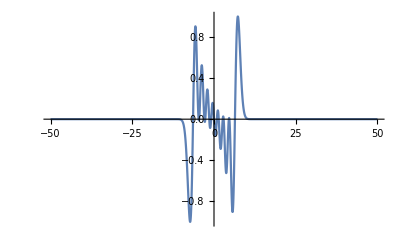

```mathematica
Plot[ϕ[6][p]H[9][p],{p,-50,50},PlotRange->All]
```